```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Get["Methods.m",Path->FileNameJoin[{Directory[],"Packages"}]]

ϵ1=10.;
ϵ2=5.;
H=12.;(*Height of first layer in angstroms*)
a= 3.904;(*unit cell size in angstroms*)
t1=.25;(*hopping parameters in eV*)
t2=.025;
MM=14;
NN=8;
β=.95;(*percent of the old distribution to keep when calculating the new distribution*)
numPartitions=20;
numStates=Ceiling[((ϵ2/ϵ1)(1/2 ArcTan[(MM a)/(2H)]-1/2 ArcTan[-((MM-2) a)/(2H)])NN (MM-1) 1/numPartitions)];

SetParameters[ϵ1,ϵ2,H, a,  t1,t2, MM, NN, β, numPartitions, numStates];
Initialize[];
firstGuess=Flatten[Table[
	 chargeDist[i,j],
	{i,1,NN},
	{j,1,MM-1}
],1];
firstGuess=totalCharge/(firstGuess//Abs//Total)firstGuess;
(*firstGuess=Import["Distribution.txt","List"];*)

,
{listvals,errorList}=SelfConsistentDistribution[firstGuess,.00005];
Export["Distribution.txt",listvals,"List"]
Export["ErrorList.txt",errorList,"List"]
PlotFullSpaceDistribution[listvals]
bandList=BandStructureList[listvals];
BandStructurePlot[0,1,bandList]
```

```mathematica
firstGuess=Import["Distribution.txt","List"]
```

{-0.00117886,-0.0022986,-0.00330307,-0.00414007,-0.0044687,0.00792916,0.0606942,0.00792916,-0.0044687,-0.00414007,-0.00330307,-0.0022986,-0.00117886,-0.000752575,-0.00146741,-0.00210867,-0.002644,-0.00301761,-0.00204668,0.00285302,-0.00204668,-0.00301761,-0.002644,-0.00210867,-0.00146741,-0.000752575,-0.00048044,-0.000936788,-0.00134616,-0.00168803,-0.00194518,-0.00210164,-0.00214292,-0.00210164,-0.00194518,-0.00168803,-0.00134616,-0.000936788,-0.00048044,-0.00030671,-0.00059804,-0.000859382,-0.00107763,-0.00124184,-0.00134378,-0.00137833,-0.00134378,-0.00124184,-0.00107763,-0.000859382,-0.00059804,-0.00030671,-0.000195802,-0.000381786,-0.000548625,-0.000687954,-0.000792786,-0.000857864,-0.000879926,-0.000857864,-0.000792786,-0.000687954,-0.000548625,-0.000381786,-0.000195802,-0.000124999,-0.00024373,-0.000350239,-0.000439186,-0.00050611,-0.000547656,-0.00056174,-0.000547656,-0.00050611,-0.000439186,-0.000350239,-0.00024373,-0.000124999,-0.0000797986,-0.000155596,-0.000223591,-0.000280374,-0.000323098,-0.00034962,-0.000358612,-0.00034962,-0.000323098,-0.000280374,-0.000223591,-0.000155596,-0.0000797986,-0.000050943,-0.0000993314,-0.000142739,-0.000178989,-0.000206264,-0.000223196,-0.000228936,-0.000223196,-0.000206264,-0.000178989,-0.000142739,-0.0000993314,-0.000050943}

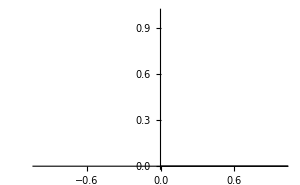

-Graphics3D-

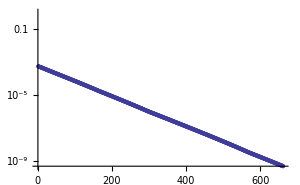

-Graphics-

-Graphics3D-

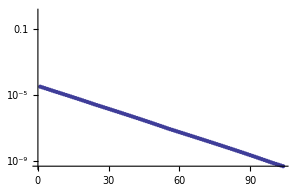

-Graphics-

-Graphics3D-

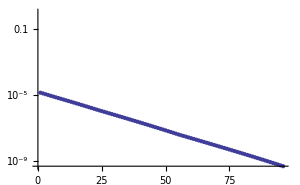

```mathematica
NN=10;
MM=20;

bandList5= Import["Tests/BandList5.txt","List"];
BandStructurePlot[0,1,bandList5]
dist5 = Import["Tests/Distribution5.txt","List"];
PlotFullSpaceDistribution[dist5]
error5 = Import["Tests/ErrorList5.txt","List"];
ListLogPlot[error5]

bandList20= Import["Tests/BandList20.txt","List"];
BandStructurePlot[0,1,bandList20]
dist20 = Import["Tests/Distribution20.txt","List"];
PlotFullSpaceDistribution[dist20]
error20 = Import["Tests/ErrorList20.txt","List"];
ListLogPlot[error20]

bandList50= Import["Tests/BandList50.txt","List"];
BandStructurePlot[0,1,bandList50]
dist50 = Import["Tests/Distribution50.txt","List"];
PlotFullSpaceDistribution[dist50]
error50 = Import["Tests/ErrorList50.txt","List"];
ListLogPlot[error50]

Partition[dist5,MM-1]//MatrixForm;
```

```mathematica
Partition[dist5,MM-1]//MatrixForm
```

(-2.06505×10^-6 | -4.07926×10^-6 | -5.99301×10^-6 | -7.75921×10^-6 | -9.33434×10^-6 | -0.0000106777 | -0.0000100419 | 0.000539437 | 0.0416046 | 0.300638 | 0.0416046 | 0.000539437 | -0.0000100419 | -0.0000106777 | -9.33434×10^-6 | -7.75921×10^-6 | -5.99301×10^-6 | -4.07926×10^-6 | -2.06505×10^-6
-1.50832×10^-6 | -2.9795×10^-6 | -4.37731×10^-6 | -5.66734×10^-6 | -6.81783×10^-6 | -7.80033×10^-6 | -8.5084×10^-6 | 0.0000163206 | 0.00183426 | 0.0129688 | 0.00183426 | 0.0000163206 | -8.5084×10^-6 | -7.80033×10^-6 | -6.81783×10^-6 | -5.66734×10^-6 | -4.37731×10^-6 | -2.9795×10^-6 | -1.50832×10^-6
-1.10168×10^-6 | -2.17623×10^-6 | -3.1972×10^-6 | -4.13944×10^-6 | -4.97976×10^-6 | -5.69746×10^-6 | -6.27473×10^-6 | -6.6583×10^-6 | -4.20521×10^-6 | 0.0000119984 | -4.20521×10^-6 | -6.6583×10^-6 | -6.27473×10^-6 | -5.69746×10^-6 | -4.97976×10^-6 | -4.13944×10^-6 | -3.1972×10^-6 | -2.17623×10^-6 | -1.10168×10^-6
-8.04671×10^-7 | -1.58953×10^-6 | -2.33524×10^-6 | -3.02346×10^-6 | -3.63723×10^-6 | -4.16144×10^-6 | -4.58318×10^-6 | -4.89205×10^-6 | -5.07968×10^-6 | -5.13832×10^-6 | -5.07968×10^-6 | -4.89205×10^-6 | -4.58318×10^-6 | -4.16144×10^-6 | -3.63723×10^-6 | -3.02346×10^-6 | -2.33524×10^-6 | -1.58953×10^-6 | -8.04671×10^-7
-5.87734×10^-7 | -1.161×10^-6 | -1.70567×10^-6 | -2.20834×10^-6 | -2.65664×10^-6 | -3.03952×10^-6 | -3.34756×10^-6 | -3.57318×10^-6 | -3.7108×10^-6 | -3.75706×10^-6 | -3.7108×10^-6 | -3.57318×10^-6 | -3.34756×10^-6 | -3.03952×10^-6 | -2.65664×10^-6 | -2.20834×10^-6 | -1.70567×10^-6 | -1.161×10^-6 | -5.87734×10^-7
-4.29282×10^-7 | -8.47994×10^-7 | -1.24583×10^-6 | -1.61298×10^-6 | -1.94042×10^-6 | -2.22008×10^-6 | -2.44507×10^-6 | -2.60986×10^-6 | -2.71038×10^-6 | -2.74417×10^-6 | -2.71038×10^-6 | -2.60986×10^-6 | -2.44507×10^-6 | -2.22008×10^-6 | -1.94042×10^-6 | -1.61298×10^-6 | -1.24583×10^-6 | -8.47994×10^-7 | -4.29282×10^-7
-3.13549×10^-7 | -6.19377×10^-7 | -9.09954×10^-7 | -1.17813×10^-6 | -1.41729×10^-6 | -1.62155×10^-6 | -1.78589×10^-6 | -1.90625×10^-6 | -1.97967×10^-6 | -2.00435×10^-6 | -1.97967×10^-6 | -1.90625×10^-6 | -1.78589×10^-6 | -1.62155×10^-6 | -1.41729×10^-6 | -1.17813×10^-6 | -9.09954×10^-7 | -6.19377×10^-7 | -3.13549×10^-7
-2.29017×10^-7 | -4.52395×10^-7 | -6.64633×10^-7 | -8.60506×10^-7 | -1.03519×10^-6 | -1.18438×10^-6 | -1.30442×10^-6 | -1.39233×10^-6 | -1.44596×10^-6 | -1.46398×10^-6 | -1.44596×10^-6 | -1.39233×10^-6 | -1.30442×10^-6 | -1.18438×10^-6 | -1.03519×10^-6 | -8.60506×10^-7 | -6.64633×10^-7 | -4.52395×10^-7 | -2.29017×10^-7
-1.67275×10^-7 | -3.3043×10^-7 | -4.8545×10^-7 | -6.28516×10^-7 | -7.56106×10^-7 | -8.65078×10^-7 | -9.52749×10^-7 | -1.01696×10^-6 | -1.05613×10^-6 | -1.06929×10^-6 | -1.05613×10^-6 | -1.01696×10^-6 | -9.52749×10^-7 | -8.65078×10^-7 | -7.56106×10^-7 | -6.28516×10^-7 | -4.8545×10^-7 | -3.3043×10^-7 | -1.67275×10^-7
-1.22178×10^-7 | -2.41347×10^-7 | -3.54574×10^-7 | -4.5907×10^-7 | -5.52262×10^-7 | -6.31855×10^-7 | -6.9589×10^-7 | -7.4279×10^-7 | -7.714×10^-7 | -7.81016×10^-7 | -7.714×10^-7 | -7.4279×10^-7 | -6.9589×10^-7 | -6.31855×10^-7 | -5.52262×10^-7 | -4.5907×10^-7 | -3.54574×10^-7 | -2.41347×10^-7 | -1.22178×10^-7)

```mathematica
ListPlot[bandList5[[1]]]
```

ListPlot::lpn: "{{0., 0.}, {0.15707963267948966, 0.0006155829702265692}, {0.3141592653589793, 0.0024471741852352125}, {0.47123889803846897, 0.005449673790565157}, {0.6283185307179586, 0.009549150281259244}, {0.7853981633974483, 0.01464466094066097}, {0.9424777960769379, 0.02061073" … "26261464019}, {2.356194490192345, 0.08535533905930492}, {2.5132741228718345, 0.09045084971872086}, {2.670353755551324, 0.09455032620941495}, {2.827433388230814, 0.09755282581474489}, {2.9845130209103035, 0.09938441702973932}, {3.141592653589793, 0.0999999999999659}}" is not a list of numbers or pairs of numbers.

ListPlot[{{0., 0.}, {0.15707963267948966, 0.0006155829702265692}, {0.3141592653589793, 0.0024471741852352125}, {0.47123889803846897, 0.005449673790565157}, {0.6283185307179586, 0.009549150281259244}, {0.7853981633974483, 0.01464466094066097}, {0.9424777960769379, 0.02061073738536834}, {1.0995574287564276, 0.02730047501302124}, {1.2566370614359172, 0.034549150281222296}, {1.413716694115407, 0.04217827674796126}, {1.5707963267948966, 0.049999999999968736}, {1.7278759594743862, 0.05782172325199042}, {1.8849555921538759, 0.0654508497187436}, {2.0420352248333655, 0.07269952498697307}, {2.199114857512855, 0.07938926261464019}, {2.356194490192345, 0.08535533905930492}, {2.5132741228718345, 0.09045084971872086}, {2.670353755551324, 0.09455032620941495}, {2.827433388230814, 0.09755282581474489}, {2.9845130209103035, 0.09938441702973932}, {3.141592653589793, 0.0999999999999659}}]

```mathematica
fib1[x_]:=fib1[x]=(fib1[x-1]+fib1[x-2])^2
fib2[x_]:=fib2[x]=fib2[x-1]^2+fib2[x-2]^2
fib1[0]=0
fib1[1]=1
fib2[0]=0
fib2[1]=1

Total[IntegerDigits[fib1[30]-fib2[30]]]//AbsoluteTiming
```

0

1

0

1

{153.89039,443589491}

```mathematica
fib2[10];//AbsoluteTiming
```

{0.,Null}